## C-Phase with KLM

```mathematica
B[θ_,ϕ_]:={{Cos[θ],-ⅇ^(+ⅈ ϕ)Sin[θ]},{+ⅇ^(-ⅈ ϕ)Sin[θ],Cos[θ]}};
θ1=π/8; ϕ1=0;
θ2=65.5302/180 π; ϕ2=0;
θ3=-π/8; ϕ3=0;
ϕ4=π;
(*η=1;*)
```

### after 50-50 Beam splitter on the left

```mathematica
{t10,b10}=B[π/4,0].{t11,b11};
```

### top

#### after Beam splitter 1 ( coupling modes 2 and 3)

```mathematica
{t21,t31}=B[θ1,ϕ1].{t22,t32};
t11=ⅇ^(-ⅈ ϕ4)t12;
```

#### after Beam splitter 2 (coupling modes 1 and 2)

```mathematica
{t12,t22}=B[θ2,ϕ2].{t13,t23};
t32=t33;
```

#### after Beam splitter 3 (coupling modes 2 and 3)

```mathematica
{t23,t33}=B[θ3,ϕ3].{t24,t34};
t13=t14;
```

#### Inefficient detectors

```mathematica
{t24,t2vac}={{√η,-√(1-η)},{+√(1-η),η}}.{t25,t2dump};
{t34,t3vac}={{√η,-√(1-η)},{+√(1-η),η}}.{t35,t3dump};
t14=t15;
```

### bottom

#### after Beam splitter 1 ( coupling modes 2 and 3)

```mathematica
{b21,b31}=B[θ1,ϕ1].{b22,b32};
b11=ⅇ^(-ⅈ ϕ4)b12;
```

#### after Beam splitter 2 (coupling modes 1 and 2)

```mathematica
{b12,b22}=B[θ2,ϕ2].{b13,b23};
b32=b33;
```

#### after Beam splitter 3 (coupling modes 2 and 3)

```mathematica
{b23,b33}=B[θ3,ϕ3].{b24,b34};
b13=b14;
```

#### Inefficient detectors

```mathematica
{b24,b2vac}={{√η,-√(1-η)},{+√(1-η),η}}.{b25,b2dump};
{b34,b3vac}={{√η,-√(1-η)},{+√(1-η),η}}.{b35,b3dump};
b14=b15;
```

### after 50-50 Beam splitter on the right

```mathematica
{t15,b15}=B[-π/4,0].{t16,b16};
```

### Operation

```mathematica
creationops=FullSimplify[CoefficientList[CoefficientList[(α+β t10)(γ+b10 δ)t21 b21,{t35,b35,t25,b25}][[1,1,2,2]],{t2dump,t3dump,b2dump,b3dump,t16,b16},{3,3,3,3,2,2}]];
fockstate=Table[√((i-1)!(j-1)!(k-1)!(l-1)!(m-1)!(n-1)!)creationops[[i,j,k,l,m,n]],{i,1,3},{j,1,3},{k,1,3},{l,1,3},{m,1,2},{n,1,2}];

P=Map[Abs[#]^2&,fockstate,{6}];
```

```mathematica
(Total[P,6]-Total[P[[1,1,1,1]],2])/Total[P[[1,1,1,1]],2]
```

(0.+0.0606602 Abs[β δ √(1-η) η]^2+0.0883883 Abs[(1. β γ-1. α δ) √(1-η) η]^2+0.0883883 Abs[(1. β γ+1. α δ) √(1-η) η]^2+0.292893 Abs[β δ (-1.+η) η]^2)/(0.0625 Abs[α γ η]^2+0.0625 Abs[β γ η]^2+0.0625 Abs[α δ η]^2+0.0625 Abs[β δ η]^2)

```mathematica
F[η_,α_,γ_,ϕT_,ϕC_]=Module[{},
β=√(1-α^2)ⅇ^(ⅈ ϕT);
δ=√(1-γ^2)ⅇ^(ⅈ ϕC);
1/(1+(Total[P,6]-Total[P[[1,1,1,1]],2])/Total[P[[1,1,1,1]],2])
];
```

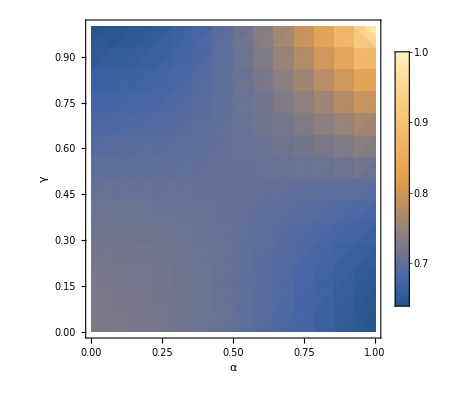

```mathematica
DensityPlot[F[0.80,α,γ,π/2,π/2],{α,0,1},{γ,0,1},PlotLegends->Automatic,PlotRange->{0,1},LabelStyle->Large,FrameLabel->Automatic]
```

```mathematica
DensityPlot[F[0.80,α,γ,0,0],{α,0,1},{γ,0,1},PlotLegends->Automatic,PlotRange->{0,1},LabelStyle->Large,FrameLabel->Automatic]
```

-Graphics-

## NSG (convention is messed up - )

### Beam splitter transformation

```mathematica
ClearAll[c11,c12,c13,c14,c21,c22,c23,c24,c31,c32,c33,c34]
```

```mathematica
B[θ_,ϕ_]:={{Cos[θ],-ⅇ^(+ⅈ ϕ)Sin[θ]},{ⅇ^(-ⅈ ϕ)Sin[θ],Cos[θ]}};(*changed r pos*)
θ1=π/8; ϕ1=0;
θ2=65.5302/180 π; ϕ2=0;
θ3=(-π/8); ϕ3=0;
ϕ4=π;
```

#### From here on we will use “cij” to denote creation operators in Mode “i” and Stage “j”

-Graphics-

### after Beam splitter 1 ( coupling modes 2 and 3)

```mathematica
{c21,c31}=B[θ1,ϕ1].{c22,c32};
c11=c12;
```

### after Beam splitter 2 (coupling modes 1 and 2)

```mathematica
{c12,c22}=B[θ2,ϕ2].{c13,c23};
c32=c33;
```

### after Beam splitter 3 (coupling modes 2 and 3)

```mathematica
{c23,c33}=B[θ3,ϕ3].{c24,c34};
c13=c14;
```

### Inefficient detectors

```mathematica
{c24,c2vac}={{√η,-√(1-η)},{+√(1-η),η}}.{c25,c2dump};
{c34,c3vac}={{√η,-√(1-η)},{+√(1-η),η}}.{c35,c3dump};
c14=c15;
```

## For ψ= n,

```mathematica
f[n_]:=Module[{creationops,fockstate},
creationops=N[CoefficientList[CoefficientList[ⅇ^(-ⅈ  n ϕ4)c11^n/(√(n!))c21,{c25,c35}][[2,1]],{c2dump,c3dump,c15},{3,3,3}]];
fockstate=Table[
√((j-1)!(k-1)!(l-1)!)creationops[[j,k,l]],
{j,1,3},{k,1,3},{l,1,3}
]
];
```

```mathematica
ClearAll[F]
```

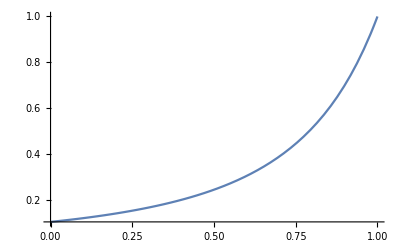

```mathematica
P=Map[Abs[#]^2&,f[0]+f[1]+f[2],{3}];

F[η_]=1/(1+(Total[P,3]-Total[P[[1,1]]])/(η 0.25));
Plot[F[η],{η,0,1}]
```

```mathematica
F[0.9]^2
```

0.491244

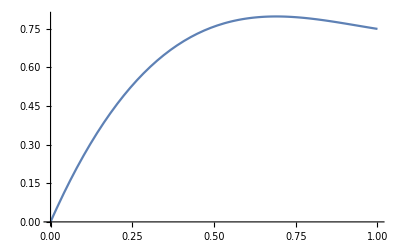

```mathematica
TotP[η_]=Total[P,3];
Plot[TotP[η],{η,0,1}]
```

```mathematica
f[0]+f[1]+f[2]//MatrixForm
```

((0.+0.5 √η
0.+0.5 √η
0.-0.5 √η) | (0.+4.91837×10^-9 √(1.-1. η) √η
0.-0.348311 √(1.-1. η) √η
0.) | (0.-0.0606602 (1.-1. η) √η
0.
0.)
(0.-0.840896 √(1.-1. η) √η
0.-0.348311 √(1.-1. η) √η
0.) | (0.+0.207107 (1.-1. η) √η
0.
0.) | (0.
0.
0.)
(0.+1.06066 (1.-1. η) √η
0.
0.) | (0.
0.
0.) | (0.
0.
0.))

```mathematica
f[1]//MatrixForm
```

((0.
0.5 √η
0.) | (4.91837×10^-9 √(1.-1. η) √η
0.
0.) | (0.
0.
0.)
(-0.840896 √(1.-1. η) √η
0.
0.) | (0.
0.
0.) | (0.
0.
0.)
(0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.))

```mathematica
f[2]//MatrixForm
```

((0.
0.
-0.5 √η) | (0.
-0.348311 √(1.-1. η) √η
0.) | (-0.0606602 (1.-1. η) √η
0.
0.)
(0.
-0.348311 √(1.-1. η) √η
0.) | (0.207107 (1.-1. η) √η
0.
0.) | (0.
0.
0.)
(1.06066 (1.-1. η) √η
0.
0.) | (0.
0.
0.) | (0.
0.
0.))

This function calculates the final coefficients of n

```mathematica
ClearAll[C0,C1,C2,C3,C4]
```

```mathematica
ClearAll[θ1,θ2,θ3,ϕ1,ϕ2,ϕ3,ϕ4]
```

```mathematica
C0=f[0]
```

0.5 √η

```mathematica
C0=f[0]
```

Cos[θ1] Cos[θ2] Cos[θ3]-ⅇ^(ⅈ ϕ1-ⅈ ϕ3) Sin[θ1] Sin[θ3]

```mathematica
C1=f[1]
```

2 c2dump ⅇ^(ⅈ ϕ2-ⅈ ϕ4) √(1-η) √η Cos[θ1] Cos[θ2] Cos[θ3]^2 Sin[θ2]-c3dump ⅇ^(ⅈ ϕ1+ⅈ ϕ2-ⅈ ϕ4) √(1-η) √η Cos[θ3]^2 Sin[θ1] Sin[θ2]-2 c3dump ⅇ^(ⅈ ϕ2+ⅈ ϕ3-ⅈ ϕ4) √(1-η) √η Cos[θ1] Cos[θ2] Cos[θ3] Sin[θ2] Sin[θ3]-2 c2dump ⅇ^(ⅈ ϕ1+ⅈ ϕ2-ⅈ ϕ3-ⅈ ϕ4) √(1-η) √η Cos[θ3] Sin[θ1] Sin[θ2] Sin[θ3]+c3dump ⅇ^(ⅈ ϕ1+ⅈ ϕ2-ⅈ ϕ4) √(1-η) √η Sin[θ1] Sin[θ2] Sin[θ3]^2+c15 (ⅇ^(-ⅈ ϕ4) √η Cos[θ1] Cos[θ2]^2 Cos[θ3]-ⅇ^(-ⅈ ϕ4) √η Cos[θ1] Cos[θ3] Sin[θ2]^2-ⅇ^(ⅈ ϕ1-ⅈ ϕ3-ⅈ ϕ4) √η Cos[θ2] Sin[θ1] Sin[θ3])

```mathematica
C1=f[1]
```

ⅇ^(-ⅈ ϕ4) Cos[θ1] Cos[θ2]^2 Cos[θ3]-ⅇ^(-ⅈ ϕ4) Cos[θ1] Cos[θ3] Sin[θ2]^2-ⅇ^(ⅈ ϕ1-ⅈ ϕ3-ⅈ ϕ4) Cos[θ2] Sin[θ1] Sin[θ3]

```mathematica
C2=f[2]
```

3 c2dump^2 ⅇ^(2 ⅈ ϕ2-2 ⅈ ϕ4) (1-η) √η Cos[θ1] Cos[θ2] Cos[θ3]^3 Sin[θ2]^2-2 c2dump c3dump ⅇ^(ⅈ ϕ1+2 ⅈ ϕ2-2 ⅈ ϕ4) (1-η) √η Cos[θ3]^3 Sin[θ1] Sin[θ2]^2-6 c2dump c3dump ⅇ^(2 ⅈ ϕ2+ⅈ ϕ3-2 ⅈ ϕ4) (1-η) √η Cos[θ1] Cos[θ2] Cos[θ3]^2 Sin[θ2]^2 Sin[θ3]-3 c2dump^2 ⅇ^(ⅈ ϕ1+2 ⅈ ϕ2-ⅈ ϕ3-2 ⅈ ϕ4) (1-η) √η Cos[θ3]^2 Sin[θ1] Sin[θ2]^2 Sin[θ3]+2 c3dump^2 ⅇ^(ⅈ ϕ1+2 ⅈ ϕ2+ⅈ ϕ3-2 ⅈ ϕ4) (1-η) √η Cos[θ3]^2 Sin[θ1] Sin[θ2]^2 Sin[θ3]+3 c3dump^2 ⅇ^(2 ⅈ ϕ2+2 ⅈ ϕ3-2 ⅈ ϕ4) (1-η) √η Cos[θ1] Cos[θ2] Cos[θ3] Sin[θ2]^2 Sin[θ3]^2+4 c2dump c3dump ⅇ^(ⅈ ϕ1+2 ⅈ ϕ2-2 ⅈ ϕ4) (1-η) √η Cos[θ3] Sin[θ1] Sin[θ2]^2 Sin[θ3]^2-c3dump^2 ⅇ^(ⅈ ϕ1+2 ⅈ ϕ2+ⅈ ϕ3-2 ⅈ ϕ4) (1-η) √η Sin[θ1] Sin[θ2]^2 Sin[θ3]^3+c15^2 (ⅇ^(-2 ⅈ ϕ4) √η Cos[θ1] Cos[θ2]^3 Cos[θ3]-2 ⅇ^(-2 ⅈ ϕ4) √η Cos[θ1] Cos[θ2] Cos[θ3] Sin[θ2]^2-ⅇ^(ⅈ ϕ1-ⅈ ϕ3-2 ⅈ ϕ4) √η Cos[θ2]^2 Sin[θ1] Sin[θ3])+c15 (4 c2dump ⅇ^(ⅈ ϕ2-2 ⅈ ϕ4) √(1-η) √η Cos[θ1] Cos[θ2]^2 Cos[θ3]^2 Sin[θ2]-2 c3dump ⅇ^(ⅈ ϕ1+ⅈ ϕ2-2 ⅈ ϕ4) √(1-η) √η Cos[θ2] Cos[θ3]^2 Sin[θ1] Sin[θ2]-2 c2dump ⅇ^(ⅈ ϕ2-2 ⅈ ϕ4) √(1-η) √η Cos[θ1] Cos[θ3]^2 Sin[θ2]^3-4 c3dump ⅇ^(ⅈ ϕ2+ⅈ ϕ3-2 ⅈ ϕ4) √(1-η) √η Cos[θ1] Cos[θ2]^2 Cos[θ3] Sin[θ2] Sin[θ3]-4 c2dump ⅇ^(ⅈ ϕ1+ⅈ ϕ2-ⅈ ϕ3-2 ⅈ ϕ4) √(1-η) √η Cos[θ2] Cos[θ3] Sin[θ1] Sin[θ2] Sin[θ3]+2 c3dump ⅇ^(ⅈ ϕ2+ⅈ ϕ3-2 ⅈ ϕ4) √(1-η) √η Cos[θ1] Cos[θ3] Sin[θ2]^3 Sin[θ3]+2 c3dump ⅇ^(ⅈ ϕ1+ⅈ ϕ2-2 ⅈ ϕ4) √(1-η) √η Cos[θ2] Sin[θ1] Sin[θ2] Sin[θ3]^2)

```mathematica
C2=f[2]
```

ⅇ^(-2 ⅈ ϕ4) Cos[θ1] Cos[θ2]^3 Cos[θ3]-2 ⅇ^(-2 ⅈ ϕ4) Cos[θ1] Cos[θ2] Cos[θ3] Sin[θ2]^2-ⅇ^(ⅈ ϕ1-ⅈ ϕ3-2 ⅈ ϕ4) Cos[θ2]^2 Sin[θ1] Sin[θ3]

```mathematica
c[0]=Cos[θ1] Cos[θ2] Cos[θ3]-ⅇ^(ⅈ ϕ1-ⅈ ϕ3) Sin[θ1] Sin[θ3];
c[1]=ⅇ^(-ⅈ ϕ4) Cos[θ1] Cos[θ2]^2 Cos[θ3]-ⅇ^(-ⅈ ϕ4) Cos[θ1] Cos[θ3] Sin[θ2]^2-ⅇ^(ⅈ ϕ1-ⅈ ϕ3-ⅈ ϕ4) Cos[θ2] Sin[θ1] Sin[θ3];
c[2]=ⅇ^(-2 ⅈ ϕ4) Cos[θ1] Cos[θ2]^3 Cos[θ3]-2 ⅇ^(-2 ⅈ ϕ4) Cos[θ1] Cos[θ2] Cos[θ3] Sin[θ2]^2-ⅇ^(ⅈ ϕ1-ⅈ ϕ3-2 ⅈ ϕ4) Cos[θ2]^2 Sin[θ1] Sin[θ3];
c[3]=ⅇ^(-3 ⅈ ϕ4) Cos[θ1] Cos[θ2]^4 Cos[θ3]-3 ⅇ^(-3 ⅈ ϕ4) Cos[θ1] Cos[θ2]^2 Cos[θ3] Sin[θ2]^2-ⅇ^(ⅈ ϕ1-ⅈ ϕ3-3 ⅈ ϕ4) Cos[θ2]^3 Sin[θ1] Sin[θ3];
c[4]=ⅇ^(4 ⅈ ϕ4) Cos[θ1] Cos[θ2]^5 Cos[θ3]-4 ⅇ^(4 ⅈ ϕ4) Cos[θ1] Cos[θ2]^3 Cos[θ3] Sin[θ2]^2-ⅇ^(ⅈ ϕ1-ⅈ ϕ3+4 ⅈ ϕ4) Cos[θ2]^4 Sin[θ1] Sin[θ3];
```

```mathematica
FullSimplify[ⅇ^(-ⅈ ϕ4)(Cos[θ2]c[0]-Cos[θ1]Cos[θ3] Sin[θ2]^2)-c[1]]
```

0

```mathematica
FullSimplify[Cos[θ2] ⅇ^(-ⅈ 2 ϕ4)(Cos[θ2]c[0]-2Cos[θ1]Cos[θ3] Sin[θ2]^2)-c[2]]
```

0

```mathematica
ClearAll[x]
```

```mathematica
Solve[ⅇ^(-ⅈ ϕ4)(Cos[θ2]x-Cos[θ1]Cos[θ3] Sin[θ2]^2)==x,x]
```

{{x→-(Cos[θ1] Cos[θ3] Sin[θ2]^2)/(ⅇ^(ⅈ ϕ4)-Cos[θ2])}}

```mathematica
ClearAll[κ]
Solve[Cos[θ2] ⅇ^(-ⅈ 2 ϕ4)(Cos[θ2]x-2Cos[θ1]Cos[θ3] Sin[θ2]^2)==ⅇ^(ⅈ κ)x,x]
```

{{x→(2 Cos[θ1] Cos[θ2] Cos[θ3] Sin[θ2]^2)/(-ⅇ^(ⅈ κ+2 ⅈ ϕ4)+Cos[θ2]^2)}}

```mathematica
κ=π/2;FullSimplify[Cos[θ2] ⅇ^(-ⅈ 2 ϕ4)(Cos[θ2](-(Cos[θ1] Cos[θ3] Sin[θ2]^2)/(ⅇ^(ⅈ ϕ4)-Cos[θ2]))-2Cos[θ1]Cos[θ3] Sin[θ2]^2)-ⅇ^(ⅈ κ)((2 Cos[θ1] Cos[θ2] Cos[θ3] Sin[θ2]^2)/(-ⅇ^(ⅈ κ+2 ⅈ ϕ4)+Cos[θ2]^2))]
```

(ⅈ ⅇ^(-2 ⅈ ϕ4) Cos[θ1] Cos[θ2]^2 (ⅈ ⅇ^(2 ⅈ ϕ4)-2 ⅇ^(ⅈ ϕ4) Cos[θ2]+Cos[θ2]^2) Cos[θ3] Sin[θ2]^2)/((ⅇ^(ⅈ ϕ4)-Cos[θ2]) (ⅇ^(2 ⅈ ϕ4)+ⅈ Cos[θ2]^2))

```mathematica
θ1=36.53/180 π; ϕ1=88.24/180 π;
θ2=62.25/180 π; ϕ2=-66.52/180 π;
θ3=-36.53/180 π; ϕ3=-11.25/180 π;
ϕ4=102.2477/180 π;
(ⅈ ⅇ^(-2 ⅈ ϕ4) Cos[θ1] Cos[θ2]^2 (ⅈ ⅇ^(2 ⅈ ϕ4)-2 ⅇ^(ⅈ ϕ4) Cos[θ2]+Cos[θ2]^2) Cos[θ3] Sin[θ2]^2)/((ⅇ^(ⅈ ϕ4)-Cos[θ2]) (ⅇ^(2 ⅈ ϕ4)+ⅈ Cos[θ2]^2))
(*ClearAll[θ1,θ2,θ3,ϕ1,ϕ2,ϕ3,ϕ4]*)
FullSimplify[ⅇ^(-ⅈ ϕ4)(Cos[θ2]c[0]-Cos[θ1]Cos[θ3] Sin[θ2]^2)-c[0]]
FullSimplify[Cos[θ2] ⅇ^(-ⅈ 2 ϕ4)(Cos[θ2]c[0]-2Cos[θ1]Cos[θ3] Sin[θ2]^2)+ⅈ c[0]]
```

-0.144828-0.134983 ⅈ

0.000143918-7.11572×10^-6 ⅈ

-0.000126376-0.000203521 ⅈ

```mathematica
(2 Cos[θ1] Cos[θ2] Cos[θ3] Sin[θ2]^2)/(-ⅇ^(ⅈ κ+2 ⅈ ϕ4)+Cos[θ2]^2)
```

-0.107423-0.49415 ⅈ

```mathematica
-(Cos[θ1] Cos[θ3] Sin[θ2]^2)/(ⅇ^(ⅈ ϕ4)-Cos[θ2])
```

0.242332+0.349414 ⅈ

```mathematica
FullSimplify[ⅇ^(-ⅈ ϕ4)(Cos[θ2]c[0]-Cos[θ1]Cos[θ3] Sin[θ2]^2)-c[1]]
FullSimplify[ⅇ^(-ⅈ ϕ4)(Cos[θ2]c[0]-Cos[θ1]Cos[θ3] Sin[θ2]^2)]-FullSimplify[c[1]]
FullSimplify[ⅇ^(-ⅈ ϕ4)(Cos[θ2]c[0]-Cos[θ1]Cos[θ3] Sin[θ2]^2)]-FullSimplify[-(Cos[θ1] Cos[θ3] Sin[θ2]^2)/(ⅇ^(ⅈ ϕ4)-Cos[θ2])]
```

```mathematica
FullSimplify[Cos[θ2] ⅇ^(-ⅈ 2 ϕ4)(Cos[θ2]((2 Cos[θ1] Cos[θ2] Cos[θ3] Sin[θ2]^2)/(-ⅇ^(ⅈ κ+2 ⅈ ϕ4)+Cos[θ2]^2))-2Cos[θ1]Cos[θ3] Sin[θ2]^2)-(2 Cos[θ1] Cos[θ2] Cos[θ3] Sin[θ2]^2)/(-ⅇ^(ⅈ κ+2 ⅈ ϕ4)+Cos[θ2]^2)]
```

-(2 (-1+ⅇ^(ⅈ κ)) Cos[θ1] Cos[θ2] Cos[θ3] Sin[θ2]^2)/(ⅇ^(ⅈ (κ+2 ϕ4))-Cos[θ2]^2)

```mathematica
κ=π/2;
```

```mathematica
ClearAll[θ1,θ2,θ3,ϕ1,ϕ2,ϕ3,ϕ4]
Assuming[-π<θ1≤ π&&-π<θ2≤ π&&-π<θ3≤ π&&-π<ϕ1≤ π&&-π<ϕ2≤ π&&-π<ϕ3≤ π &&ϕ4∈Reals,Reduce[-(Cos[θ1] Cos[θ3] Sin[θ2]^2)/(ⅇ^(ⅈ ϕ4)-Cos[θ2])-(2 Cos[θ1] Cos[θ2] Cos[θ3] Sin[θ2]^2)/(-ⅇ^(ⅈ κ+2 ⅈ ϕ4)+Cos[θ2]^2),{θ1,θ2,θ3,ϕ1,ϕ2,ϕ3,ϕ4}]]
```

C[1]∈ℤ&&((ⅈ ⅇ^(3 ⅈ ϕ4)-ⅈ ⅇ^(2 ⅈ ϕ4) Cos[θ2]-ⅇ^(ⅈ ϕ4) Cos[θ2]^2+Cos[θ2]^3≠0&&(θ1==-π/2+2 π C[1]||θ1==π/2+2 π C[1]||θ3==-π/2+2 π C[1]||θ3==π/2+2 π C[1]))||(Cos[θ2]≠0&&(ϕ4==-ⅈ (2 ⅈ π C[1]+Log[-ⅈ Cos[θ2]-√(-1+ⅈ) Cos[θ2]])||ϕ4==-ⅈ (2 ⅈ π C[1]+Log[-ⅈ Cos[θ2]+√(-1+ⅈ) Cos[θ2]])))||(-ⅈ+ⅈ ⅇ^(ⅈ ϕ4)-ⅇ^(2 ⅈ ϕ4)+ⅇ^(3 ⅈ ϕ4)≠0&&θ2==2 π C[1])||(1+ⅇ^(ⅈ ϕ4)-ⅈ ⅇ^(2 ⅈ ϕ4)-ⅈ ⅇ^(3 ⅈ ϕ4)≠0&&θ2==π+2 π C[1]))

```mathematica
func1[θ1_,θ2_,θ3_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=-(Cos[θ1] Cos[θ3] Sin[θ2]^2)/(ⅇ^(ⅈ ϕ4)-Cos[θ2]);
func2[θ1_,θ2_,θ3_,ϕ1_,ϕ2_,ϕ3_,ϕ4_,κ_]:=(2 Cos[θ1] Cos[θ2] Cos[θ3] Sin[θ2]^2)/(-ⅇ^(ⅈ κ+2 ⅈ ϕ4)+Cos[θ2]^2);
```

```mathematica
Abs[func1[36.53/180 π,62.25/180 π,-36.53/180 π,88.24/180 π,-66.52/180 π,-11.25/180 π,102.2477/180 π]]^2
Arg[func1[36.53/180 π,62.25/180 π,-36.53/180 π,88.24/180 π,-66.52/180 π,-11.25/180 π,102.2477/180 π]]
```

0.180815

-0.96442

```mathematica
Abs[func2[36.53/180 π,62.25/180 π,-36.53/180 π,88.24/180 π,-66.52/180 π,-11.25/180 π,102.2477/180 π,π/2]]^2
Arg[func2[36.53/180 π,62.25/180 π,-36.53/180 π,88.24/180 π,-66.52/180 π,-11.25/180 π,102.2477/180 π,π/2]]
```

0.180775

-0.964197

```mathematica
ClearAll[ϕ4]
Solve[(-(ⅇ^(ⅈ ϕ4) Cos[θ1] Cos[θ3] Sin[θ2]^2)/(-1+ⅇ^(ⅈ ϕ4) Cos[θ2])+ⅇ^(ⅈ ϕ4) (Cos[θ1] Cos[2 θ2] Cos[θ3]-ⅇ^(ⅈ (ϕ1-ϕ3)) Cos[θ2] Sin[θ1] Sin[θ3])==0),{ϕ4}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ4→-1.78427+0.000179084 ⅈ}}

```mathematica
(180*-1.7842713551404346)/π
```

-102.231

```mathematica
θ1=36.53/180 π; ϕ1=-88.24/180 π;
θ2=62.25/180 π; ϕ2=(+66.52)/180 π;
θ3=-36.53/180 π; ϕ3=(+11.25)/180 π;
ϕ4=-102.2477/180 π;
FullSimplify[ⅇ^(-ⅈ ϕ4)(Cos[θ2]c[0]-Cos[θ1]Cos[θ3] Sin[θ2]^2)]-FullSimplify[-(Cos[θ1] Cos[θ3] Sin[θ2]^2)/(ⅇ^(ⅈ ϕ4)-Cos[θ2])]
```

0.0000344006-0.0000447131 ⅈ

```mathematica
FullSimplify[c[1]/c[0]]
```

1.00018-0.000287714 ⅈ

```mathematica
FullSimplify[c[2]/c[1]]
```

-0.000274979-0.999849 ⅈ

```mathematica
{{Abs[c[0]],Arg[c[0]]},{Abs[c[1]],Arg[c[1]]},{Abs[c[2]],Arg[c[2]]},{Abs[c[3]],Arg[c[3]]},{Abs[c[4]],Arg[c[4]]}}//MatrixForm
```

```mathematica
({{0.42520368625607846, -0.9647014619658453}, {0.42527984045929274, -0.9644137995148738}, {0.4252158259147413, 0.6066575472669711}, {0.3064902424046062, 2.3274380437251097}, {0.1935037978883042, 2.3715272904118225}})
```

```mathematica
{{1,0},{Abs[c[1]]/Abs[c[0]],Arg[c[1]]-Arg[c[0]]},{Abs[c[2]]/Abs[c[0]],Arg[c[2]]-Arg[c[0]]},{Abs[c[3]]/Abs[c[0]],Arg[c[3]]-Arg[c[0]]},{Abs[c[4]]/Abs[c[0]],Arg[c[4]]-Arg[c[0]]}}//MatrixForm
```

(1 | 0
1.00018 | 0.000287662
1.00003 | 1.57136
0.720808 | 3.29214
0.455085 | 3.33623)

```mathematica
Arg[C2]-Arg[C1]
```

-1.57107

```mathematica
(*-π<θ1≤ π&&-π<θ2≤ π&&-π<θ3≤ π&&-π<ϕ1≤ π&&-π<ϕ2≤ π&&-π<ϕ3≤ π &&ϕ4∈Reals &&*)
```

```mathematica
Reduce[Cos[θ2]≠0&&func1[θ1,θ2,θ3,ϕ1,ϕ2,ϕ3,ϕ4]==func2[θ1,θ2,θ3,ϕ1,ϕ2,ϕ3,ϕ4,π],{θ1,θ2,θ3,ϕ1,ϕ2,ϕ3,ϕ4}]
```

C[1]∈ℤ&&((Cos[θ2] (-1+ⅇ^(ⅈ ϕ4) Cos[θ2]-ⅇ^(2 ⅈ ϕ4) Cos[θ2]^2+ⅇ^(3 ⅈ ϕ4) Cos[θ2]^3)≠0&&(θ1==-π/2+2 π C[1]||θ1==π/2+2 π C[1]||θ3==-π/2+2 π C[1]||θ3==π/2+2 π C[1]))||(Cos[θ2]≠0&&(ϕ4==-ⅈ (2 ⅈ π C[1]+Log[(1-√2) Sec[θ2]])||ϕ4==-ⅈ (2 ⅈ π C[1]+Log[(1+√2) Sec[θ2]])))||(-1+ⅇ^(ⅈ ϕ4)-ⅇ^(2 ⅈ ϕ4)+ⅇ^(3 ⅈ ϕ4)≠0&&θ2==2 π C[1])||(1+ⅇ^(ⅈ ϕ4)+ⅇ^(2 ⅈ ϕ4)+ⅇ^(3 ⅈ ϕ4)≠0&&θ2==π+2 π C[1]))

```mathematica
Reduce[Element[ϕ4,Reals]&&(C[1]∈Integers&&((-1+ⅇ^(ⅈ ϕ4) Cos[θ2]-ⅇ^(2 ⅈ ϕ4) Cos[θ2]^2+ⅇ^(3 ⅈ ϕ4) Cos[θ2]^3≠0&&(θ1==-π/2+2 π C[1]||θ1==π/2+2 π C[1]||θ3==-π/2+2 π C[1]||θ3==π/2+2 π C[1]))||(Cos[θ2]≠0&&(ϕ4==-ⅈ (2 ⅈ π C[1]+Log[(1-√2) Sec[θ2]])||ϕ4==-ⅈ (2 ⅈ π C[1]+Log[(1+√2) Sec[θ2]])))||(-1+ⅇ^(ⅈ ϕ4)-ⅇ^(2 ⅈ ϕ4)+ⅇ^(3 ⅈ ϕ4)≠0&&θ2==2 π C[1])||(1+ⅇ^(ⅈ ϕ4)+ⅇ^(2 ⅈ ϕ4)+ⅇ^(3 ⅈ ϕ4)≠0&&θ2==π+2 π C[1]))),{θ1,θ2,θ3,ϕ1,ϕ2,ϕ3,ϕ4}]
```

### NS_-1 Gate

```mathematica
θ1=π/8; ϕ1=0;
θ2=65.5302/180 π; ϕ2=0;
θ3=-π/8; ϕ3=0;
ϕ4=π;
```

```mathematica
c[0]
```

0.5

```mathematica
Chop[N[C0]]
```

0.5 √η

```mathematica
Collect[N[Chop[C1]],c15]
```

0.5 c15 √η-0.840896 c2dump √(1.-1. η) √η+4.91837×10^-9 c3dump √(1.-1. η) √η

```mathematica
Collect[N[Chop[C2]],c15^2]
```

c15 (-0.492586 c2dump √(1.-1. η) √η-0.492586 c3dump √(1.-1. η) √η)-0.5 c15^2 √η+1.06066 c2dump^2 (1.-1. η) √η+0.292893 c2dump c3dump (1.-1. η) √η-0.0606602 c3dump^2 (1.-1. η) √η

```mathematica
CoefficientList[Chop[Simplify[(C0-0.5 √η)+c15 (C1-0.5 √η)+c15^2(C2+0.5 √η)]],{c15,c2dump,c3dump}]//MatrixForm
```

((-7.06032×10^-9 √η
0
0) | (0
0
0) | (0
0
0)
(-0.5 √η
4.91837×10^-9 √(1-η) √η
0) | (-0.840896 √(1-η) √η
0
0) | (0
0
0)
(1. √η
0
-1.06066 (0.057191-0.057191 η) √η) | (0
-1.06066 (-0.276142+0.276142 η) √η
0) | (-1.06066 √η (-1.+1. η)
0
0)
(0
-0.492586 √(1-η) √η
0) | (-0.492586 √(1-η) √η
0
0) | (0
0
0)
(-0.5 √η
0
0) | (0
0
0) | (0
0
0))

```mathematica
CoefficientList[Chop[Simplify[(C0-0.5 √η)+c15 (C1-0.5 √η)+c15^2(C2+0.5 √η)]],{c15,c2dump,c3dump}]
```

```mathematica
C0
```

0.5

```mathematica
C1
```

0.5

```mathematica
C2
```

-0.5

```mathematica
C3
```

0.328427

```mathematica
C4
```

C4

### NS_i Gate

```mathematica
θ1=36.53/180 π; ϕ1=88.24/180 π;
θ2=62.25/180 π; ϕ2=-66.52/180 π;
θ3=-36.53/180 π; ϕ3=-11.25/180 π;
ϕ4=102.2477/180 π;
```

```mathematica
Abs[C0]
Arg[C0]
```

0.425204

0.964701

```mathematica
Abs[C1]
Arg[C1]
```

0.42528

0.964414

```mathematica
Abs[C2]
Arg[C2]
```

0.425216

-0.606658

```mathematica
Abs[C3]
Arg[C3]
```

0.30649

2.09673

```mathematica
Abs[C4]
Arg[C4]
```

0.193504

-2.37153

#### Results

```mathematica
0.30649024240460615/0.4252158259147413
```

0.720787

```mathematica
-0.9644137995148738+2.09673075464374
```

```mathematica
1.132316955128866/π
```

0.360428